```mathematica
SetDirectory@NotebookDirectory[];
```

## Data

```mathematica
numQb=4;
numGt=numQb^2;
numR=numQb+2*numGt;

SecSize=1000;
numSec=10;
SamSize=numSec*SecSize;

fileT=File["data/HS-U.dat"];
USall = Import[fileT];
CS={};HS={};
Do[(
fileT=File["data/HS-C-"<>ToString[i]<>".dat"];
CST=Import[fileT];
CS=Join[CS,Transpose[CST]];
fileT=File["data/HS-H-"<>ToString[i]<>".dat"];
HST=Import[fileT];
HS=Join[HS,Transpose[HST]];
),{i,1,numSec}];
CSall=Transpose[CS];HSall=Transpose[HS];
```

## Error

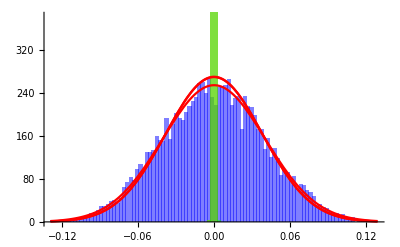

```mathematica
US=USall[[1,1;;SamSize]];
CS1=CSall[[1]];CS2=CSall[[3]];
HS1=HSall[[1]];HS2=HSall[[3]];

scale=1;
xMax=Max[Abs[Join[US,CS1,HS1]]]/scale;
xMin=-xMax;
dx=(xMax-xMin)/100;
HUplot=Histogram[US,{xMin,xMax,dx},ChartStyle->Opacity[.5,Blue]];
HCplot=Histogram[CS1,{xMin,xMax,dx},ChartStyle->Opacity[.5,Orange]];
HHplot=Histogram[HS1,{xMin,xMax,dx},ChartStyle->Opacity[.5,Green]];
σ=Sqrt[Moment[US,2]];
yMax=Ceiling[1.5*SamSize*dx*PDF[NormalDistribution[0,σ],0]];
NDUplot=Plot[SamSize*dx*PDF[NormalDistribution[0,σ],x]//Evaluate,{x,xMin,xMax},PlotStyle->{Red},PlotRange->All];
σ=Sqrt[Moment[CS2,1]];
NDCplot=Plot[SamSize*dx*PDF[NormalDistribution[0,σ],x]//Evaluate,{x,xMin,xMax},PlotStyle->{Red},PlotRange->All];
σ=Sqrt[Moment[HS2,1]];
NDHplot=Plot[SamSize*dx*PDF[NormalDistribution[0,σ],x]//Evaluate,{x,xMin,xMax},PlotStyle->{Red},PlotRange->All];
Show[HUplot,HCplot,HHplot,NDUplot,NDCplot,NDHplot,PlotRange->{{xMin,xMax},{0,yMax}}]
```

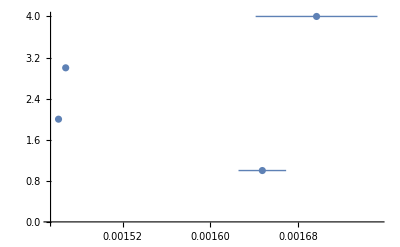

0.0016470.000022

0.001461612

0.001468110

0.001700.00006

```mathematica
μU=Moment[US,2];
σU=Sqrt[(Moment[US,4]-Moment[US,2]^2)/SamSize];
μC=Moment[CS2,1];
σC=Sqrt[(Moment[CS2,2]-Moment[CS2,1]^2)/SamSize];
μH=Moment[HS2,1];
σH=Sqrt[(Moment[HS2,2]-Moment[HS2,1]^2)/SamSize];
μHC=numR*μH-(numR-1)*μC;
σHC=Sqrt[(numR*σH)^2+((numR-1)*σC)^2];
ListPlot[{{Around[μU,σU],1},{Around[μC,σC],2},{Around[μH,σH],3},{Around[μHC,σHC],4}}]
Around[μU,σU]
Around[μC,σC]
Around[μH,σH]
Around[μHC,σHC]
```

## Fidelity

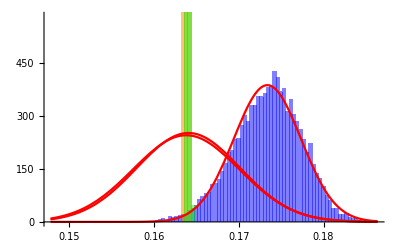

```mathematica
US=USall[[2,1;;SamSize]];
CS1=CSall[[2]];CS2=CSall[[4]];
HS1=HSall[[2]];HS2=HSall[[4]];

scale=1;
μ=(Moment[US,1]+Moment[CS1,1]+Moment[HS1,1])/3;
xMax=μ+Max[Abs[Join[US-μ,CS1-μ,HS1-μ]]]/scale;
xMin=2μ-xMax;
dx=(xMax-xMin)/100;
HUplot=Histogram[US,{xMin,xMax,dx},ChartStyle->Opacity[.5,Blue]];
HCplot=Histogram[CS1,{xMin,xMax,dx},ChartStyle->Opacity[.5,Orange]];
HHplot=Histogram[HS1,{xMin,xMax,dx},ChartStyle->Opacity[.5,Green]];
μ=Moment[US,1];
σ=Sqrt[Moment[US,2]-μ^2];
yMax=Ceiling[1.5*SamSize*dx*PDF[NormalDistribution[0,σ],0]];
NDUplot=Plot[SamSize*dx*PDF[NormalDistribution[μ,σ],x]//Evaluate,{x,xMin,xMax},PlotStyle->{Red},PlotRange->All];
μ=Moment[CS1,1];
σ=Sqrt[Moment[CS2,1]-μ^2];
NDCplot=Plot[SamSize*dx*PDF[NormalDistribution[μ,σ],x]//Evaluate,{x,xMin,xMax},PlotStyle->{Red},PlotRange->All];
μ=Moment[HS1,1];
σ=Sqrt[Moment[HS2,1]-μ^2];
NDHplot=Plot[SamSize*dx*PDF[NormalDistribution[μ,σ],x]//Evaluate,{x,xMin,xMax},PlotStyle->{Red},PlotRange->All];
Show[HUplot,HCplot,HHplot,NDUplot,NDCplot,NDHplot,PlotRange->{{xMin,xMax},{0,yMax}}]
```

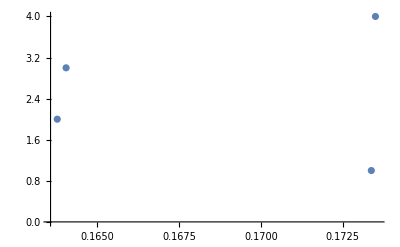

0.173370.00004

0.163789113

0.164058812

0.173500.00006

```mathematica
μU=Moment[US,1];
σU=Sqrt[(Moment[US,2]-Moment[US,1]^2)/SamSize];
μC=Total[CS1]/SamSize;
σC=Sqrt[(Moment[CS1,2]-Moment[CS1,1]^2)/SamSize];
μH=Total[HS1]/SamSize;
σH=Sqrt[(Moment[HS1,2]-Moment[HS1,1]^2)/SamSize];
μHC=numR*μH-(numR-1)*μC;
σHC=Sqrt[(numR*σH)^2+((numR-1)*σC)^2];
ListPlot[{{Around[μU,σU],1},{Around[μC,σC],2},{Around[μH,σH],3},{Around[μHC,σHC],4}}]
Around[μU,σU]
Around[μC,σC]
Around[μH,σH]
Around[μHC,σHC]
```